```mathematica
Clear[xb1,xb2,kT]
xb1=3/2;xb2=2;kT=4012/1000; (*bond length and thermal force*)
kaF[ka_,f_]:=ka*Exp[f*xb1/kT]; (*off rate under force for APC-Ag bond*)
kbF[kb_,f_]:=kb*Exp[f*xb2/kT];(* off rate under force for BCR-Ag bond*)
etaF[ka_, kb_, f_]:=1/(1+kbF[kb, f]/kaF[ka, f]);
lamda[ka_,kb_,f_]:=kaF[ka, f]+kbF[kb,f];(*total off rates*)
```

```mathematica
Clear[n0, ea, eb, de]
TmeanFE[n0_, ea_,eb_,F_:0]:=Sum[1/(i*lamda[Exp[-ea],Exp[-eb],F/i]),{i,1,n0}];
DklNag[n0_, ea_,eb_, de_]:=n0 (Log[1+Exp[eb-ea+de]]-Log[1+Exp[eb-ea]]-de/(1+Exp[ea-eb]))
DklTau[n0_, ea_, eb_, de_]:=Module[{},Clear[lmd1, lmd2];
lmd1=lamda[Exp[-ea], Exp[-eb], 0];
lmd2=lamda[Exp[-ea], Exp[-eb-de], 0];
Log[lmd1/lmd2]-(lmd1-lmd2)TmeanFE[n0, ea, eb]-1+1/n0 +(n0-1)NIntegrate[lmd2 Exp[-lmd2 t](1-Exp[-lmd1 t])^n0/(1-Exp[-lmd2 t]), {t, 0, Infinity}]
]

DklNag[10, 0, 0, 1.0]
N[DklTau[10, 0, 0, 1], 5]
```

1.20115

0.411427

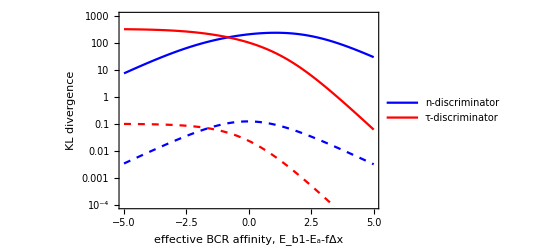

```mathematica
Show[
LogPlot[{
DklNag[100, 0, ebx-2.5, 5],
DklTau[100, 0, ebx-2.5, 5]
}, {ebx, -5, 5},PlotRange->{0.0001, 1000}, PlotStyle->{Blue,Red}, PlotLegends->Placed[{"n-discriminator", "τ-discriminator"},{0.3, 0.15}]],
LogPlot[{
DklNag[100, 0, ebx, 0.1],
DklTau[100, 0, ebx, 0.1]
}, {ebx, -5, 5},PlotRange->{0.0001, 100}, PlotStyle->{{Blue, Dashed},{Red, Dashed}}],
Frame->True,
FrameLabel->{"effective BCR affinity, E_b1-E_a-fΔx", "KL divergence"},
FrameStyle->Directive[16]
]
```

```mathematica
TimeFisherInfoIndepF[100, 1, 1, 0]
```

4.86361

```mathematica
TimeFisherInfoIndepF[100, 1, Exp[2], 0]
```

15.0928

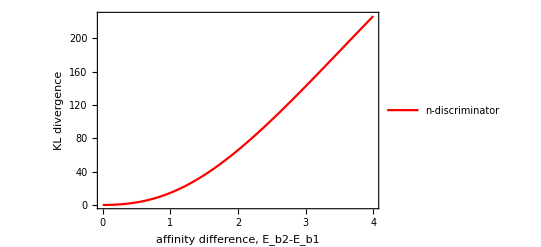

```mathematica
Show[
Plot[{
(*DklNag[100, 0, -6, dex],*)
DklTau[100, 0, -6, dex]
}, {dex, 0, 4},PlotRange->All, PlotStyle->{Blue,Red}, PlotLegends->Placed[{"n-discriminator", "τ-discriminator"},{0.2, 0.8}]],
(*Plot[{
0.5 *NagFisherInfo[100, 1, Exp[2], 0]*dex^2,
0.5 *TimeFisherInfoIndepF[100, 1, Exp[2], 0]*dex^2
}, {dex, 0, 1}, PlotStyle->{{Blue, Dashed}, {Red, Dashed}}],*)
Frame->True,
FrameLabel->{"affinity difference, E_b2-E_b1", "KL divergence"},
FrameStyle->Directive[16]
]
```

```mathematica
Table[i, {22, 50, 2}]
```

Table::itraw: Raw object 22 cannot be used as an iterator.

Table[i,{22,50,2}]

```mathematica
nlist =Join[ Table[i, {i, 1, 20}], Table[i, {i, 22, 50, 2}], Table[i, {i, 60, 200, 10}],Table[i, {i, 250, 1000, 50}]];
```

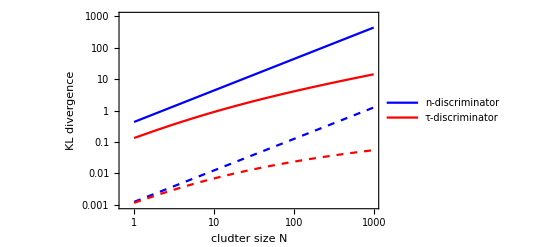

```mathematica
Show[
ListLogLogPlot[{
Table[{nlist[[i]],DklNag[nlist[[i]], 0, 0, 2]}, {i,1, Length[nlist] }],
Table[{nlist[[i]],DklTau[nlist[[i]], 0, 0, 2]}, {i,1, Length[nlist] }]
}, PlotRange->{0.001, 1000}, PlotStyle->{Blue,Red},Filling->False, Joined->True, PlotLegends->Placed[{"n-discriminator", "τ-discriminator"},{0.3, 0.85}]],
ListLogLogPlot[{
Table[{nlist[[i]],DklNag[nlist[[i]], 0, 0, 0.1]}, {i,1, Length[nlist] }],
Table[{nlist[[i]],DklTau[nlist[[i]], 0, 0, 0.1]}, {i,1, Length[nlist] }]
}, PlotRange->{0.001, 10}, PlotStyle->{{Dashed,Blue},{Dashed,Red}},Filling->False, Joined->True],

Frame->True,
FrameLabel->{"cludter size N", "KL divergence"},
FrameStyle->Directive[16]
]
```

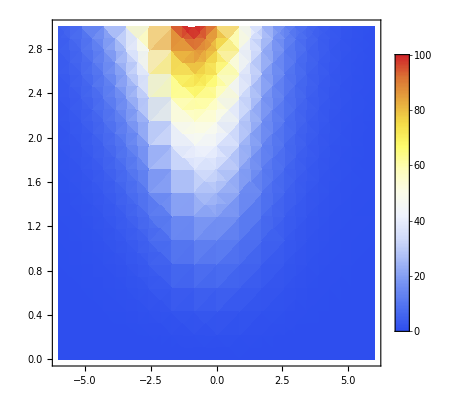

```mathematica
DensityPlot[DklNag[100, 0, eb1, de], {eb1, -6,6}, {de, 0, 3},PlotRange->{0, 100},  PlotLegends->Automatic,  ColorFunction->"TemperatureMap"]
```

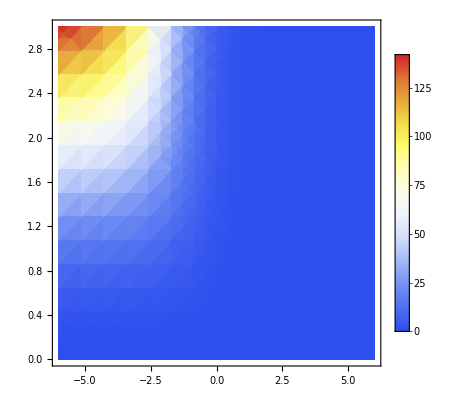

```mathematica
DensityPlot[DklTau[100, 0, eb1, de], {eb1, -6,6}, {de, 0, 3},PlotRange->{0, 150}, PlotLegends->Automatic, ColorFunction->"TemperatureMap"]
```

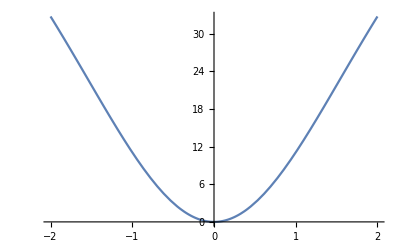

```mathematica
Plot[DklNag[100, 0, 0-de, 0+de], {de, -2, 2}]
```